```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Das hier ist der Versuch, den Winkel der Rotation offen zu lassen, also bei verschiedenen Stärken des Treibens dennoch das externe BFeld konstant zu lassen, indem man verschiedene Ganzzahlen für die jeweiligen Rotationen des Blochvektors wählt. Scheint zu funktionieren.*)
f1=((2*π*m1*N)^2-θ1^2)*l2^2;
f2=((2*π*m2*N)^2-(π-θ1)^2)*l1^2;
t1=Table[{f1},{m1,2,2},{l2,1,1}]
t2=Table[{f2},{m2,1,1},{l1,2,2}]
```

{{{16 N^2 π^2-θ1^2}}}

{{{4 (4 N^2 π^2-(π-θ1)^2)}}}

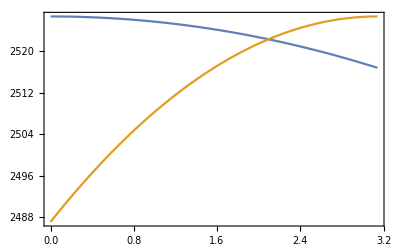

```mathematica
Plot[{t1/.N->4,t2/.N->4},{θ1,0,π},Frame->True]
```

```mathematica
(*Das hier ist der Versuch, trotz der Kontrolle verschiedener Kohlenstoffspins mit unterschiedlicher Kopplungskonstante dennoch das externe BFeld konstant zu lassen, indem man verschiedene Ganzzahlen für die jeweiligen Rotationen des Blochvektors wählt.*)
n1=1;
n2=1;
g1=(m2^2-(2*n2+1)^2/(4*M2^2)^2)*l1^2*x^2;
g2=(m1^2-(2*n1+1)^2/(4*M1^2)^2)*l2^2;
t1=Table[{g1},{m2,1,3},{l1,1,3}]
t2=Table[{g2},{m1,1,3},{l2,1,3}]
```

{{{(1-9/(16 M2^4)) x^2},{4 (1-9/(16 M2^4)) x^2},{9 (1-9/(16 M2^4)) x^2}},{{(4-9/(16 M2^4)) x^2},{4 (4-9/(16 M2^4)) x^2},{9 (4-9/(16 M2^4)) x^2}},{{(9-9/(16 M2^4)) x^2},{4 (9-9/(16 M2^4)) x^2},{9 (9-9/(16 M2^4)) x^2}}}

{{{1-9/(16 M1^4)},{4 (1-9/(16 M1^4))},{9 (1-9/(16 M1^4))}},{{4-9/(16 M1^4)},{4 (4-9/(16 M1^4))},{9 (4-9/(16 M1^4))}},{{9-9/(16 M1^4)},{4 (9-9/(16 M1^4))},{9 (9-9/(16 M1^4))}}}

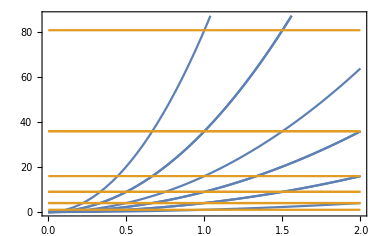

```mathematica
(*Also das scheint auch zu funktionieren.*)
Plot[{t1/.M2->4,t2/.M1->4},{x,0,2},Frame->True]
```

```mathematica
(*Todo: jeweilige Gatterzeit ausrechnen, und Bext.*)
```